## Ch 13 Exercises

### (7)

```mathematica
u1[v_,Vstar_,Ustar_,p_]=Ustar+Sqrt[-(p[v]-p[Vstar])/(v-Vstar)](v-Vstar)
```

Ustar+(v-Vstar) √((-p[v]+p[Vstar])/(v-Vstar))

```mathematica
u2[v_,Vstar_,Ustar_,p_]=Ustar-Sqrt[-(p[v]-p[Vstar])/(v-Vstar)](v-Vstar)
```

Ustar-(v-Vstar) √((-p[v]+p[Vstar])/(v-Vstar))

```mathematica
p1[v_]=-Exp[v];
```

```mathematica
Vstar1=1; Ustar1=1;
```

```mathematica
Vstar2=3;Ustar2=4;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

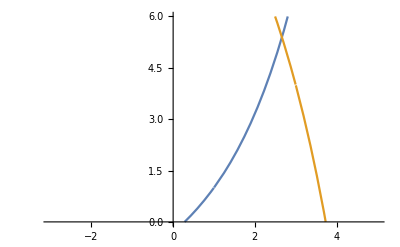

```mathematica
Plot[{u1[v,Vstar1,Ustar1,p1],u2[v,Vstar2,Ustar2,p1]},{v,-3,5},PlotRange->{0,6}]
```

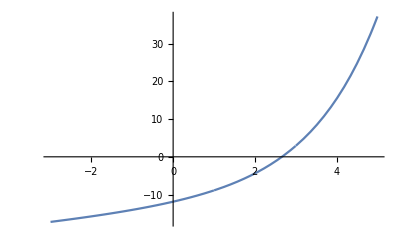

```mathematica
Plot[u1[v,Vstar1,Ustar1,p1]-u2[v,Vstar2,Ustar2,p1],{v,-3,5}, PlotRange->Full]
```

```mathematica
NSolve[u1[v,Vstar1,Ustar1,p1]-u2[v,Vstar2,Ustar2,p1]==0,v]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-3+√((-ⅇ^3+ⅇ^v)/(-3+v)) (-3+v)+√((-ⅇ+ⅇ^v)/(-1+v)) (-1+v)==0,v]

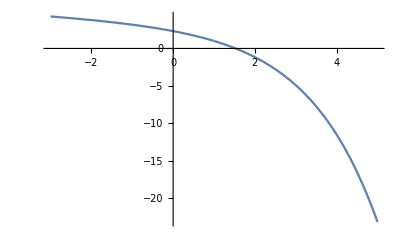

```mathematica
Plot[u2[v,Vstar1,Ustar1,p1],{v,-3,5}]
```

```mathematica
Vstar2=3;Ustar2=4;
```

```mathematica
Plot[u1[v,Vstar2,Ustar1,p2],{v,-3,5}]
```